## Exercise 9—Second-Order Equations

## Exercise 1

Classify these second-order equations:

5y''(t)+y'(t)+2y(t)=0				(1)

y''(t)+3y(t)+t^2 y(t)=e^t				(2)

y''(t)^2+y'(t)=e^t					(3)

### Solution

(1) is a linear homogeneous second-order differential equation with constant coefficients.

(2) is a linear nonhomogeneous second-order differential equation.

(3) is a nonlinear nonhomogeneous second-order differential equation.

## Exercise 2

Determine the characteristic polynomial for the following differential equation:

4y''(t)+6y'(t)+2y(t)=0

### Solution

Assume the answer is of the form y(t)=e^(λ t) for some constant λ and substitute this form into the differential equation:

```mathematica
(4*y''[t]+6y'[t]+2y[t]==0)/.y->Function[t,Exp[λ t]]
```

Because e^(λ t)≠0 for any real value of λ and t, this term can be canceled and the characteristic equation is seen to be:

4 λ^2+6λ+2=0

## Exercise 3

Find the general solution to the following differential equation:

4y''(t)+6y'(t)+2y(t)=0

### Solution

In Exercise 2, you found the characteristic equation associated with this differential equation to be the following:

4 λ^2+6λ+2=0

Solve the characteristic equation for λ:

```mathematica
{Subscript[λ, 1],Subscript[λ, 2]}=λ/.Solve[4 λ^2+6λ+2==0,λ]
```

The possible values for λ are -1/2,-1. Thus the solutions must be:

```mathematica
y1[t_]=Exp[Subscript[λ, 1] t]
```

and:

```mathematica
y2[t_]=Exp[Subscript[λ, 2] t]
```

Verify that these answers are indeed correct by substituting them back into the differential equation:

```mathematica
(4y''[t]+6y'[t]+2y[t]==0)/.y->Function[t,y1[t]]
(4y''[t]+6y'[t]+2y[t]==0)/.y->Function[t,y2[t]]
```

The general solution is any linear combination of these two solutions:

```mathematica
genSol[t_]=Subscript[C, 1] y1[t]+Subscript[C, 2] y2[t]
```

Verify that the general solution satisfies the differential equation as well:

```mathematica
(4y''[t]+6y'[t]+2y[t]==0)/.y->Function[t,genSol[t]]//Simplify
```

Finally, confirm the result found with DSolveValue:

```mathematica
DSolveValue[4y''[t]+6y'[t]+2y[t]==0,y[t],t]//Expand
```

## Exercise 4

Solve the following initial value problem:

4y''(t)+6y'(t)+2y(t)=0

y(0)=5

y'(0)=1/2

### Solution

In Exercise 3 the general solution for this differential equation was found to be:

```mathematica
genSol[t_]:=Subscript[C, 1] ⅇ^-t +Subscript[C, 2] ⅇ^(-t/2)
```

Use the first initial condition to set up one algebraic equation involving the two coefficients:

```mathematica
eqn1=genSol[0]==5
```

Use the second initial condition to set up another algebraic equation:

```mathematica
eqn2=genSol'[0]==1/2
```

Solve the system of two algebraic equation for the coefficients:

```mathematica
constants=Solve[{eqn1,eqn2},{Subscript[C, 1],Subscript[C, 2]}][[1]]
```

Thus the solution to the initial value problem is:

```mathematica
genSol[x]/.constants
```

Verify this result with DSolveValue:

```mathematica
DSolveValue[{4y''[t]+6y'[t]+2y[t]==0,y'[0]==1/2,y[0]==5},y[t],t]//Expand
```

## Exercise 5

Plot the solutions to this initial value problem for the various combinations of initial conditions:

4y''(t)+6y'(t)+2y(t)=0

y(0)=-1,1

y'(0)=1,0,-1

### Solution

Because the Wolfram Language is symbolic, it is possible to compute the constants for any initial condition:

y(0)=a

y'(0)=b

Define the general solution to the differential equation that was found in Exercise 3:

```mathematica
genSol[t_]:=Subscript[C, 1] ⅇ^-t +Subscript[C, 2] ⅇ^(-t/2)
```

Use the general solution to set up a system of two algebraic equations using the general initial conditions y(0)=a and y'(0)=b:

```mathematica
eqn1=genSol[0]==a
eqn2=genSol'[0]==b
```

Solve the system of equations to find the a-dependent and b-dependent values for C_1 and C_2:

```mathematica
Solve[{eqn1,eqn2},{Subscript[C, 1],Subscript[C, 2]}]
```

Therefore computing solutions for different initial conditions can be a relatively simple process, since you have found the value of the coefficients for any value of the initial conditions.

Define a function that takes the initial values as inputs and can calculate the values of the constants corresponding to those initial conditions:

```mathematica
initialValueSolution[t_,a_,b_]:=(-a-2 b)ⅇ^-t +2 (a+b)ⅇ^(-t/2)
```

Now to plot the solutions with the different initial conditions, write the following command:

```mathematica
Plot[{
initialValueSolution[t,1,-1],
initialValueSolution[t,1,0],
initialValueSolution[t,1,1],
initialValueSolution[t,-1,-1],
initialValueSolution[t,-1,0],
initialValueSolution[t,-1,1]
},{t,0,10},]
```

## Exercise 10—Linear Homogeneous Equations

## Exercise 1

Find all solutions of the following differential equation:

y''(x)+4y'(x)+3y(x)=0

### Solution

The solutions are determined by first solving the characteristic polynomial:

```mathematica
{Subscript[λ, 1],Subscript[λ, 2]}=λ/.Solve[λ^2+4λ+3==0,λ]
```

Therefore two solutions are e^(-3x) and e^(-1x):

```mathematica
y1[x_]:=Exp[Subscript[λ, 1] x]
y2[x_]:=Exp[Subscript[λ, 2] x]
```

Use the Wronskian Determinant theorem to define every solution to the differential equation:

```mathematica
Wronskian[{y1[x],y2[x]},x]
```

Because the Wronskian Determinant is nonzero, every solution to the differential equation must be a linear combination of these two functions.

Therefore, all solutions to the differential equation are the function:

y(x)=C[1]e^(-3x)+C[2]e^-x

Confirm this result with DSolveValue:

```mathematica
DSolveValue[y''[x]+4y'[x]+3y[x]==0,y[x],x]
```

## Exercise 2

Calculate the Wronskian Determinant of the two functions:

y_1(t)=15x e^x

y_2(t)=9 x^2 e^x

### Solution

First, define two functions in Mathematica:

```mathematica
y1[x_]:=15x Exp[x]
y2[x_]:=9 x^2 Exp[x]
```

Next, use the function Wronskian to calculate the Wronskian Determinant:

```mathematica
Wronskian[{y1[x],y2[x]},x]
```

These functions have a nonzero Wronskian Determinant except for when x=0.

If both of these functions satisfied the same differential equation for x>0 or x<0, then these two functions would form a fundamental solution set.

## Exercise 3

Calculate the Wronskian Determinant of the two functions:

y_1(t)=x^2

y_2(t)=x^3

### Solution

First, define two functions in Mathematica:

```mathematica
y1[x_]:=x^2
y2[x_]:=x^3
```

Next, use the function Wronskian to calculate the Wronskian Determinant:

```mathematica
Wronskian[{y1[x],y2[x]},x]
```

These functions have a nonzero Wronskian Determinant except for when x=0.

If both of these functions satisfied the same differential equation for x>0 or x<0, then these two functions would form a fundamental solution set.

## Exercise 4

Verify that the two functions:

y_1(x)=x^(1/2 (1-√5))

y_2(x)=x^(1/2 (1+√5))

form a fundamental solution set to the equation:

x^2 y''(x)-y(x)=0

### Solution

First, define the two functions in the Wolfram Language:

```mathematica
y1[x_]:=x^(1/2(1-√5))
y2[x_]:=x^(1/2(1+√5))
```

Calculate the Wronskian Determinant:

```mathematica
Wronskian[{y1[x],y2[x]},x]
```

Since the Wronskian Determinant is nonzero for all values of x, these two functions will form a fundamental solution set to a differential equation as long as both functions satisfy that same equation.

Verify that these functions both solve the differential equation:

```mathematica
(x^2 y''[x]-y[x]==0)/.y->Function[x,y1[x]]//Simplify
```

```mathematica
(x^2 y''[x]-y[x]==0)/.y->Function[x,y2[x]]//Simplify
```

Therefore, by the Wronskian Determinant theorem, it can be concluded that these functions form a fundamental solution set to the differential equation.

Therefore, all solutions to the differential equation are the function:

y(x)=C[1]x^(1/2 (1-√5))+C[2]x^(1/2 (1+√5))

## Exercise 5

Verify that the two functions:

y_1(x)=e^x

y_2(x)=x e^x

form a fundamental solution set to the equation:

y''(x)-2y'(x)+y(x)=0

### Solution

First, define the two functions in the Wolfram Language:

```mathematica
y1[x_]:=Exp[x]
y2[x_]:=x Exp[x]
```

```mathematica
Wronskian[{y1[x],y2[x]},x]
```

Since the Wronskian Determinant is nonzero for all real values of x, these two functions will form a fundamental solution set to a differential equation as long as both functions satisfy that same equation.

It remains to check that these functions both solve the differential equation:

```mathematica
(y''[x]-2y'[x]+y[x]==0)/.y->Function[x,y1[x]]//Simplify
```

```mathematica
(y''[x]-2y'[x]+y[x]==0)/.y->Function[x,y2[x]]//Simplify
```

Therefore, by the Wronskian Determinant theorem, these functions form a fundamental solution set to the differential equation.

As a result, all solutions to the differential equation will take the following form:

y(x)=C[1]e^x+C[2]x e^x

## Exercise 11—Complex Characteristic Roots

## Exercise 1

Find the solution to the following initial value problem using the characteristic equation:

y''(t)+y'(t)+3y(t)=0

### Solution

This is a second-order homogeneous differential equation with constant coefficients, so the solutions can be determined by solving the characteristic equation:

```mathematica
{Subscript[λ, 1],Subscript[λ, 2]}=λ/.Solve[λ^2+λ+3==0,λ]//Expand
```

For the case when complex roots are present of the form λ=r±ⅈγ, the general solution is:

y(t) =C_1 e^(r t)cos(γ t)+C_2 e^(r t)sin(γ t)

Therefore two fundamental solutions are:

y_1(t)=e^(-1/2t)cos((√11)/2 t)

y_2(t)=e^(-1/2t)sin((√11)/2 t)

The general solution can then be written as:

y(t)=C_1 e^(-1/2t)cos((√11)/2 t)+C_2 e^(-1/2t)sin((√11)/2 t)

Confirm this result with DSolveValue:

```mathematica
DSolveValue[y''[t]+y'[t]+3y[t]==0,y[t],t]
```

## Exercise 2

Evaluate:

e^(2π k i)

where k is any integer

### Solution

From Euler’s formula, remember that:

e^(ⅈ x)=cos(x)+ⅈ sin(x)

Therefore expand e^(2π k i) using Euler’s formula, and simplify, assuming k is an integer:

```mathematica
Simplify[Cos[2π k]+I Sin[2 π k],k∈Integers]
```

This makes sense because sin(2π k)=0 for every integer k, and cos(2π k)= 1 for every integer k.

## Exercise 3

Find the solution to the following initial value problem using the characteristic equation:

y''(t)+y(t)=0

y(0)=1

y'(0)=2

### Solution

This is a second-order homogeneous differential equation with constant coefficients, so the solutions can be determined by solving the characteristic equation:

```mathematica
Solve[λ^2+1==0,λ]
```

For the case when complex roots are present of the form λ=r±ⅈγ, the general solution is:

y(t) =C_1 e^(r t)cos(γ t)+C_2 e^(r t)sin(γ t)

Therefore, with r=0 and γ=1, two fundamental solutions are:

y_1(t)=cos(t)

y_2(t)=sin(t)

The general solution is then a linear combination of these solutions:

```mathematica
genSol[t_]:=Subscript[C, 1] Cos[t]+Subscript[C, 2] Sin[t]
```

Use the initial conditions to set up a system of two algebraic equations involving the constants:

```mathematica
eqn1=genSol[0]==1
eqn2=genSol'[0]==2
```

Therefore, the solution to the initial value problem must be:

y(t)=cos(t)+2 sin(t)

Confirm this result with DSolveValue:

```mathematica
DSolveValue[{y''[t]+y[t]==0,y[0]==1,y'[0]==2},y[t],t]
```

## Exercise 4

Describe the asymptotic behavior as t->∞ of solutions to second-order linear homogeneous differential equations when the characteristic polynomial has complex roots.

### Solution

For the case when complex roots are present of the form λ=r±ⅈγ, the general solution is:

y(t)=C_1 e^(r t)cos(γ t)+C_2 e^(r t)sin(γ t)

Assume that C_1 and C_2 are nonzero.

The cos(γ t) and sin(γ t) terms are bounded between -1 and 1.

When r is negative, the e^(r t) terms will converge to 0 as t→∞, so there will be oscillations from the cos(γ t) and sin(γ t) terms, but with decaying amplitudes due to the e^(r t) terms.

When r is positive, the solutions will oscillate indefinitely, but with rapidly increasing amplitudes of oscillation due to the e^(r t) terms.

Notice that the asymptotic behavior is completely determined by the value of r:

```mathematica
Solve[a λ^2+b λ +c==0,λ]
```

When examining the quadratic formula, determine that r=-b/(2a).

Thus, for differential equations of the form:

a y''(t)+b y'(t)+c  y(t)=0

when -b/(2a)<0, the solution converges to 0 and for -b/(2a)>0, the solution will diverge.

## Exercise 5

Find the solution to the following initial value problem using the characteristic equation:

1/2 y''(t)+4y'(t)+25/2

y(0)=3

y'(0)=2

### Solution

This is a second-order homogeneous differential equation with constant coefficients, so the solutions can be determined by solving the characteristic equation:

```mathematica
{Subscript[λ, 1],Subscript[λ, 2]}=λ/.Solve[1/2 λ^2+4λ+25/2==0,λ]
```

For the case when complex roots are present of the form λ=r±ⅈγ, the general solution is:

y(t)=C_1 e^(r t)cos(γ t)+C_2 e^(r t)sin(γ t)

Therefore, with r=-4 and γ=3, two fundamental solutions are:

y_1(t)=e^(-4 t)cos(3t)

y_2(t)=e^(-4 t)sin(3t)

The general solution is then a linear combination of these solutions:

```mathematica
genSol[t_]:=Subscript[C, 1] Exp[-4t] Cos[3t] + Subscript[C, 2] Exp[-4t]Sin[3t]
```

Use the initial conditions to set up a system of two algebraic equations involving the constants:

```mathematica
eqn1=genSol[0]==3
eqn2=genSol'[0]==2
```

Solve the system of equations for the coefficients:

```mathematica
constants=Solve[{eqn1,eqn2},{Subscript[C, 1],Subscript[C, 2]}][[1]]
```

Therefore, the solution to the initial value problem must be:

```mathematica
genSol[x]/.constants
```

Confirm this result with DSolveValue:

```mathematica
dSol=DSolveValue[{1/2 y''[t]+4y'[t]+25/2 y[t]==0,y[0]==3,y'[0]==2},y[t],t]//Expand
```

Plotting the solution, it is seen that the result agrees with the conclusion from the previous exercises that when r<0, the solutions tend to converge to 0:

```mathematica
Plot[dSol,{t,0,3},PlotRange->All]
```

## Exercise 12—Repeated Characteristic Roots

## Exercise 1

Find the general solution to this differential equation:

y''(t)+2y'(t)+y(t)=0

### Solution

This is a second-order homogeneous differential equation with constant coefficients, so the solutions can be determined by solving the characteristic equation:

```mathematica
Solve[λ^2+2λ+1==0,λ]
```

For the case when repeated roots are present, the general solution is:

y(t)=C_1 e^(r t)+C_2 t e^(r t)

Therefore, with r=-1, the two solutions are:

y_1(t)=e^-t

y_2(t)=t e^-t

The general solution is then a linear combination of these solutions:

y(t)=C_1 e^-t+C_2 t e^-t

Confirm this result with DSolveValue:

```mathematica
DSolveValue[y''[t]+2y'[t]+y[t]==0,y[t],t]
```

## Exercise 2

Find the solution to the following initial value problem using the characteristic equation:

4y''(x)+12y'(x)+9y(x)=0

y(0)=1

y'(0)=2

### Solution

This is a second-order homogeneous differential equation with constant coefficients, so the solutions can be determined by solving the characteristic equation:

```mathematica
Solve[4 λ^2+12λ+9==0,λ]
```

For the case when repeated roots are present, the general solution is:

y(x)=C_1 e^(r x)+C_2 x e^(r x)

Therefore, with r=-3/2, two solutions are:

y_1(x)=e^(-3/2x)

y_2(x)=x e^(-3/2x)

The general solution is then a linear combination of these solutions:

```mathematica
genSol[x_]:=Subscript[C, 1] Exp[- 3x/2] + Subscript[C, 2] x Exp[-3 x/2]
```

Use the initial conditions to set up a system of two algebraic equations involving the constants:

```mathematica
eqn1=genSol[0]==1
eqn2=genSol'[0]==2
```

Solve the system of equations for the coefficients:

```mathematica
constants=Solve[{eqn1,eqn2},{Subscript[C, 1],Subscript[C, 2]}][[1]]
```

The solution to the initial value problem must then be:

```mathematica
genSol[x]/.constants
```

Confirm this result with DSolveValue:

```mathematica
DSolveValue[{4y''[x]+12y'[x]+9y[x]==0,y[0]==1,y'[0]==2},y[x],x]//Expand
```

## Exercise 3

Consider the following initial value problem:

4y''(x)+12y'(x)+9y(x)=0

y(0)=a

y'(0)=b

The solutions for different initial values are shown in the following:

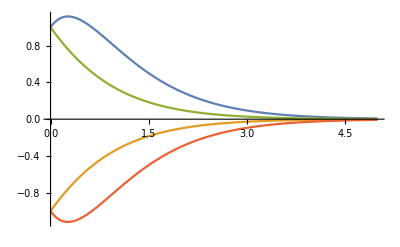

```mathematica
CellPrint[ExpressionCell[Plot[{1/2 ⅇ^(-3 x/2) (2 +5x),1/2 ⅇ^(-3 x/2) (-2 +-  x),1/2 ⅇ^(-3 x/2) (2 + x),1/2 ⅇ^(-3 x/2) (-2 -5x)},{x,0,5}],GeneratedCell->False,"Output"]]
```

All of the solutions seem to converge to zero.

Prove that for any given initial condition, the solution converges to 0 as x→∞.

### Solution

In Exercise 2 it was shown that the solution to this initial value problem is given as:

```mathematica
genSol[x_]:=Subscript[C, 1] ⅇ^(-3 x/2)+Subscript[C, 2] ⅇ^(-3 x/2) x
```

Use the Limit function to find the behavior at as x->∞:

```mathematica
Limit[genSol[x],x->∞]
```

This problem can also be solved explicitly.

First, define a system of algebraic equations using the initial conditions:

```mathematica
eqn1=genSol[0]==a;
eqn2=genSol'[0]==b;
```

Solve the system of equations for the coefficients:

```mathematica
constants=Solve[{eqn1,eqn2},{Subscript[C, 1],Subscript[C, 2]}][[1]]
```

The solution to the initial value problem must then be:

```mathematica
genSol[x]/.constants
```

The limit of the solution to the initial value problem for a general set of initial conditions is zero:

```mathematica
Limit[(genSol[x]/.constants),x->Infinity]
```

Thus for every initial condition, the solution converges to zero.

## Exercise 4

Completely describe the long-term behavior of solutions to second-order linear homogeneous differential equations when the characteristic polynomial has repeated roots.

### Solution

For the case when repeated roots are present, the general solution is:

y(x)=C_1 e^(r x)+C_2 x e^(r x)

The term C_2 x e^(r x) behaves like e^(r x) for large values of x.

Thus it can be concluded that solutions behave as C e^(r x) as x->∞.

When r is negative, solutions eventually converge to 0 as x→∞.

When r is positive, the solution diverges to positive or negative infinity depending on the values of the constants.

The asymptotic behavior is completely determined by the value of r:

```mathematica
Solve[a λ^2+b λ +c==0,λ]
```

When the roots are repeated, it is found that they are both r=-b/(2a).

Thus, for differential equations of the form:

a y''(x)+b y'(x)+c y(x)=0

when -b/(2a)<0 the equation converges to 0, while for  -b/(2a)>0 the solution will diverge to positive or negative infinity.

## Exercise 5

Find and plot the solution to the following initial value problem using the characteristic equation:

y''(x)-10y'(x)+25y(x)=0

y(0)=4

y'(0)=2

### Solution

This is a second-order homogeneous differential equation with constant coefficients, so the solutions can be determined by solving the characteristic equation:

```mathematica
Solve[λ^2-10 λ+25==0,λ]
```

For the case when repeated roots are present, the general solution is:

y(x)=C_1 e^(r x)+C_2 x e^(r x)

Therefore, with r=5 the two solutions are:

y_1(x)=e^(5x)

y_2(x)=x e^(5x)

The general solution is any linear combination of these solutions:

```mathematica
genSol[x_]:=Subscript[C, 1] Exp[5 x]+Subscript[C, 2] x Exp[5 x]
```

Define a system of algebraic equations using the initial conditions:

```mathematica
eqn1=genSol[0]==4;
eqn2=genSol'[0]==2;
```

Solve the system of equations for the coefficients:

```mathematica
constants=Solve[{eqn1,eqn2},{Subscript[C, 1],Subscript[C, 2]}][[1]]
```

The solution to the initial value problem must then be:

```mathematica
genSol[x]/.constants
```

Confirm this result with DSolveValue:

```mathematica
dSol=DSolveValue[{y''[x]-10y'[x]+25y[x]==0,y[0]==4,y'[0]==2},y[x],x]//Expand
```

Visualize the solution to the initial value problem:

```mathematica
Plot[dSol,{x,0,1/10},PlotRange->All]
```